## Initialization

Try to model exactly the solution for two cells

```mathematica
Clear["Global`*"];
```

```mathematica
S[x_]:= Coff +(Con-Coff)*x;
g[x1_,x2_]:= S[x1] + fN*S[x2];
```

Typical value of f(d):

```mathematica
fdval = Exp[R-a0]/a0 Sinh[R] /. {R-> 0.1, a0->0.5}
```

0.134288

System parameters

```mathematica
params = {fN-> fdval, n-> 2};
params2 = {k-> 13, Coff-> 1, Con-> 28, fN-> fdval, n-> 2};
```

Phase diagram parameters

```mathematica
Constart = 1;
Conmax= 30;
kstart = 1;
kmax = 30;
ds=0.2;
```

## Solutions with X_1=X_2, analytical solution (only n=1,2,3,4,5)

Fixed point equation 
 -(C_on-1)^2 X^3+[(C_on-1)^2 -2 (C_on-1)]X^2 + [2(C_on-1) - 1 - K^2/((1 + f(d))^2)]X + 1 =0

Δ = 18 a b c d - 4 b^3 d + b^2 c^2 - 4 a c^3 - 27 a^2 d^2;
Δ > 0: three distinct roots

```mathematica
a=  -(Con-1)^2;
b = (Con-1)^2 -2 (Con-1);
c =  2(Con-1) - 1 - k^2/((1 + fN)^2);
d = 1;
Δ = 18 a b c d - 4 b^3 d + b^2 c^2 - 4 a c^3 - 27 a^2 d^2;
Apart[Δ]
```

(-(12 (-1+Con)^2)/(1+fN)^2+(2 (-3+Con)^2 (-1+Con)^2)/(1+fN)^2+(48 (-1+Con)^3)/(1+fN)^2+(18 (-3+Con) (-1+Con)^3)/(1+fN)^2-(4 (-3+Con)^2 (-1+Con)^3)/(1+fN)^2-(48 (-1+Con)^4)/(1+fN)^2) k^2+(-(12 (-1+Con)^2)/(1+fN)^4+((-3+Con)^2 (-1+Con)^2)/(1+fN)^4+(24 (-1+Con)^3)/(1+fN)^4) k^4-(4 (-1+Con)^2 k^6)/(1+fN)^6

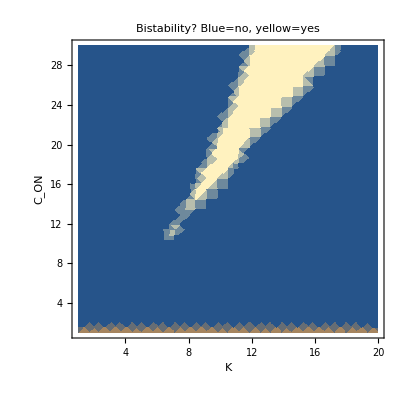

```mathematica
DensityPlot[ Sign[Δ /. params2] , {k,1,20},{Con,1,30},PlotLabel->"Bistability? Blue=no, yellow=yes", FrameLabel-> {"K", "C_ON"}]
```

Note that Δ is a quintic equation in C_on, therefore it is not easy to find the roots of Δ=0 which gives the range where we have three real solutions. However, we can solve for k^2 (quadratic equation).

```mathematica
ksol=Solve[-(4 (-1+Con)^2 Con^3 k2)/(1+fN)^2+((-1+Con)^2 (-27+18 Con+Con^2) k2^2)/(1+fN)^4-(4 (-1+Con)^2 k2^3)/(1+fN)^6==0, k2];
```

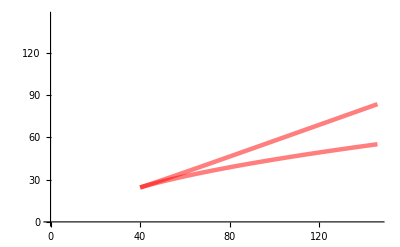

```mathematica
plot1 = Plot[ (k2 /. ksol[[2;;]] )^(1/2)/. params , {Con,Constart,Conmax}, PlotStyle-> { Thickness[0.01], RGBColor[1,0,0, 0.5]}];
plot1b = Plot[ ((k2 /. ksol[[2;;]] )^(1/2)-kstart)/ds/. params /. {Con-> Constart+idx*ds}, {idx,1, (Conmax-Constart)/ds+1}, PlotStyle-> {Thickness[0.008], RGBColor[1,0,0, 0.5]}];
Show[plot1b, AxesOrigin-> {0,0}, PlotRange-> {{0,(Conmax-1)/ds+1},{0, (kmax-1)/ds+1}}]
```

#### B = 0 line

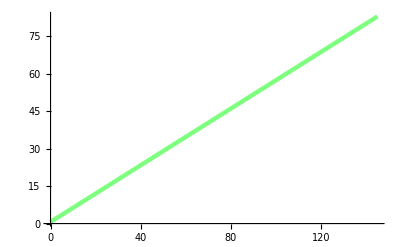

```mathematica
Kfunc = (Con+1)/2(1+fN);
plot0 = Plot[Kfunc /. params, {Con, Constart,Conmax}, PlotStyle-> {RGBColor[0,1,1, 0.8], Thickness[0.01], Dashed}, AxesOrigin-> {0,0}];
plot0b = Plot[(Kfunc-kstart)/ds/. params /. {Con-> Constart+idx*ds}, {idx,0, (Conmax-Constart)/ds}, PlotStyle-> {RGBColor[0, 1,0, 0.5],Thickness[0.008]}, AxesOrigin-> {0,0}, PlotRange-> All]
```

```mathematica
LinguisticAssistant
```

## Full phase diagram

### Compute number of stable fixed points

Calculate fixed points

```mathematica
params2 = {k-> 10, Coff-> 1, Con-> 18, fN-> fdval, n-> 2};
nsol=NSolve[{x1 == g[x1, x2]^n/(k^n+g[x1, x2]^n),x2 == g[x2, x1]^n/(k^n+g[x2, x1]^n), x1 ∈ Reals, x2∈ Reals} /. params2, {x1,x2}]
```

{{x1→0.653724,x2→0.653724},{x1→0.202489,x2→0.202489},{x1→0.02614,x2→0.02614}}

Calculate Jacobian matrix. General expression for eigenvalues is not useful.

```mathematica
J=FullSimplify/@{{D[g[x1, x2]^n/(k^n+g[x1, x2]^n)-x1,x1],D[g[x1, x2]^n/(k^n+g[x1, x2]^n)-x1,x2]},{ D[g[x2, x1]^n/(k^n+g[x2, x1]^n)-x2,x1],D[g[x2, x1]^n/(k^n+g[x2, x1]^n)-x2,x2]}};
J  // MatrixForm
```

(-1-((Coff-Con) k^n n (Coff (1+fN-x1-fN x2)+Con (x1+fN x2))^(-1+n))/((k^n+(Coff (1+fN-x1-fN x2)+Con (x1+fN x2))^n)^2) | -((Coff-Con) fN k^n n (Coff (1+fN-x1-fN x2)+Con (x1+fN x2))^(-1+n))/((k^n+(Coff (1+fN-x1-fN x2)+Con (x1+fN x2))^n)^2)
-((Coff-Con) fN k^n n (Coff (1+fN-fN x1-x2)+Con (fN x1+x2))^(-1+n))/((k^n+(Coff (1+fN-fN x1-x2)+Con (fN x1+x2))^n)^2) | -1-((Coff-Con) k^n n (Coff (1+fN-fN x1-x2)+Con (fN x1+x2))^(-1+n))/((k^n+(Coff (1+fN-fN x1-x2)+Con (fN x1+x2))^n)^2))

Numerically calculate eigenvalues at the fixed points. Verify that they are stable (Re[λ] < 0 for all λ).

```mathematica
Jn =FullSimplify[J  /. params2];
(* Show Jacobian*) TableForm@Table[ Jn /. nsol[[i]] // MatrixForm, {i, 1, Length[nsol]}]; 
ev=Table[ Eigenvalues[Jn  /. nsol[[i]]], {i, 1, Length[nsol]}];
Print["Eigenvalues: (λ1, λ2)=", MatrixForm/@ev ];
stability = MapThread[And, Transpose@Negative[ev]];
Print["Eigenvalues positive?"];
TableForm[stability, TableHeadings->{Table[StringReplace["Eigenvector number = %d", "%d" ->  ToString[i]], {i,1,Length[nsol]}], {"Positive?"}}]
```

Eigenvalues: (λ1, λ2)={(-0.515065
-0.36462),(0.23597
-0.0566815),(-0.542648
-0.400761)}

Eigenvalues positive?

Eigenvector number = 1 | True
Eigenvector number = 2 | False
Eigenvector number = 3 | True

Obtain the number of stable fixed points

```mathematica
nstable = Total[Boole/@stability];
Print["Number of stable fixed points = ", nstable];
```

Number of stable fixed points = 2

```mathematica
θ = 0.5 ;(*Threshold*)
stablesol = nsol[[Flatten@Position[stability, True]]];
boolesol=Map[(#>θ)&, ({x1,x2}/.stablesol),{2}];
If[
Length[boolesol] == 1, (*If only one solution*)
Print@Boole@First@Apply[(#1 && #2)&,  boolesol, 2 ],(* Low or high solution? low=0, high=1 *)
Print@nstable;
]
```

2

### Modular function

```mathematica
data2=Range[1];
nstablefunc[kin_,Conin_,fdin_, idx_]:=Module[{params2,nsol,J,Jn,ev,stability,tab,nstable,θ,stablesol,boolesol,data2temp},
Print["K = ", kin, ", Con= ", Conin, ", f(d)=", fdin];
params2 = {k-> kin, Coff-> 1, Con-> Conin, fN-> fdin, n-> 2};
nsol=NSolve[{x1 == g[x1, x2]^n/(k^n+g[x1, x2]^n),x2 == g[x2, x1]^n/(k^n+g[x2, x1]^n), x1 ∈ Reals, x2∈ Reals} /. params2, {x1,x2}];
(*allsol[[idx]]=nsol;*)
J=FullSimplify/@{{D[g[x1, x2]^n/(k^n+g[x1, x2]^n)-x1,x1],D[g[x1, x2]^n/(k^n+g[x1, x2]^n)-x1,x2]},{ D[g[x2, x1]^n/(k^n+g[x2, x1]^n)-x2,x1],D[g[x2, x1]^n/(k^n+g[x2, x1]^n)-x2,x2]}};
Jn =FullSimplify[J  /. params2];
(* Show Jacobian*) 
TableForm@Table[ Jn /. nsol[[i]] // MatrixForm, {i, 1, Length[nsol]}]; 
ev=Table[ Eigenvalues[Jn  /. nsol[[i]]], {i, 1, Length[nsol]}];
(*Print["Eigenvalues: (λ1, λ2)=", MatrixForm/@ev ];*)

stability = MapThread[And, Transpose@Negative[ev]];
(*Print["Eigenvalues positive?"];
tab=TableForm[stability, TableHeadings->{Table[StringReplace["Eigenvector number = %d", "%d" ->  ToString[i]], {i,1,Length[nsol]}], {"Positive?"}}];
Print[tab];*)
nstable = Total[Boole/@stability];
(*Print["Number of stable fixed points = ", nstable];*)

(* Low and high solutions*)
θ = 0.5 ;(*Threshold*)
stablesol = nsol[[Flatten@Position[stability, True]]];
boolesol=Map[(#>θ)&, ({x1,x2}/.stablesol),{2}];
If[
Length[boolesol] == 1, (*If only one solution*)
data2temp=Boole@First@Apply[(#1 && #2)&,  boolesol, 2 ],(* Low or high solution? low=0, high=1 *)
data2temp=nstable;
];
data2[[idx]] = data2temp;
Print[ "Stable fixed pts.=",nstable, ", data2=",data2temp];
(*Print["Solution (low=0, high=1, multiple=n) ", data2[[idx]]];*)
];
ndata =1;
allsol=Range[ndata];
nstablefunc[1.2, 1,fdval, 1]
```

K = 1.2, Con= 1, f(d)=0.134288

Stable fixed pts.=1, data2=0

### Construct phase diagram

#### Example

```mathematica
Kall = {10, 15};
Conall = {15, 15};
fdall = {fdval, fdval};
ndata =Length[Kall];
allsol=Range[ndata];
MapThread[nstablefunc, {Kall, Conall, fdall, Range[ndata]}]
```

K = 10, Con= 15, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 15, Con= 15, f(d)=0.134288

Set::partw: Part 2 of data2⟦2⟧ does not exist.

Stable fixed pts.=1, data2=0

{Null,Null}

Find low and high fixed points (old method for full calculation)

Important: set threshold θ for defining whether state is “low” or “high”

```mathematica
θ = 0.5 ;(*Threshold*)
Length/@({x1,x2}/.allsol);
allboole=Map[(#>θ)&, ({x1,x2}/.allsol),{3}];
data2= data;
For[i=1, i≤ Length[allsol], i++, 
If[
Length[allboole[[i]]] == 1, (*If only one solution*)
data2[[i]]=Boole@First@Apply[(#1 && #2)&,  allboole[[i]], 2 ],(* Low or high solution? low=0, high=1 *)
data2[[i]]=data[[i]] (*Else bistability, denote as 2*)
];
]
```

ReplaceAll::reps: {1,2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {1,2} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Part::partd: Part specification data⟦1⟧ is longer than depth of object.

Set::partd: Part specification data2⟦i⟧ is longer than depth of object.

Part::partd: Part specification data⟦2⟧ is longer than depth of object.

Set::partd: Part specification data2⟦i⟧ is longer than depth of object.

#### Full calculation

```mathematica
Klist = Range[kstart,kmax,ds];
Conlist = Range[Constart,Conmax, ds];
Kall=Flatten[ConstantArray[Klist, {1,Length[Conlist]}]] ;
Conall=Flatten[Transpose[First@ConstantArray[Conlist, {1,Length[Klist]}]]];
fdall = Flatten[ConstantArray[fdval,{1,Length[Kall]}]];
ndata =Length[Kall];
data2=Range[ndata];
data=MapThread[nstablefunc, {Kall, Conall, fdall, Range[ndata]}];
```

K = 1., Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=1

K = 1.2, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 1.4, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 1.6, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 1.8, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 2., Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 2.2, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 2.4, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 2.6, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 2.8, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 3., Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 3.2, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 3.4, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 3.6, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 3.8, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 4., Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 4.2, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 4.4, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 4.6, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 4.8, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 5., Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 5.2, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 5.4, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 5.6, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 5.8, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 6., Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 6.2, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 6.4, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 6.6, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 6.8, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 7., Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 7.2, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 7.4, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 7.6, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 7.8, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 8., Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 8.2, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 8.4, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 8.6, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 8.8, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 9., Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 9.2, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 9.4, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 9.6, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 9.8, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 10., Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 10.2, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 10.4, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 10.6, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 10.8, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 11., Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 11.2, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 11.4, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 11.6, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 11.8, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 12., Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 12.2, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 12.4, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 12.6, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 12.8, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 13., Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 13.2, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 13.4, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 13.6, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 13.8, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 14., Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 14.2, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 14.4, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 14.6, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 14.8, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 15., Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 15.2, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 15.4, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 15.6, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 15.8, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 16., Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 16.2, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 16.4, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 16.6, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 16.8, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 17., Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 17.2, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 17.4, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 17.6, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 17.8, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 18., Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 18.2, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 18.4, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 18.6, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 18.8, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 19., Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 19.2, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 19.4, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 19.6, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 19.8, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 20., Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 20.2, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 20.4, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 20.6, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 20.8, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 21., Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 21.2, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 21.4, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 21.6, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 21.8, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 22., Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 22.2, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 22.4, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 22.6, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 22.8, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 23., Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 23.2, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 23.4, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 23.6, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 23.8, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 24., Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 24.2, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 24.4, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 24.6, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 24.8, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 25., Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 25.2, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 25.4, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 25.6, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 25.8, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 26., Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 26.2, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 26.4, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 26.6, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 26.8, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 27., Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 27.2, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 27.4, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 27.6, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 27.8, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 28., Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 28.2, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 28.4, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 28.6, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 28.8, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 29., Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 29.2, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 29.4, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 29.6, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 29.8, Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 30., Con= 1., f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 1., Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=1

K = 1.2, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=1

K = 1.4, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 1.6, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 1.8, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 2., Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 2.2, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 2.4, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 2.6, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 2.8, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 3., Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 3.2, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 3.4, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 3.6, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 3.8, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 4., Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 4.2, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 4.4, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 4.6, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 4.8, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 5., Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 5.2, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 5.4, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 5.6, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 5.8, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 6., Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 6.2, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 6.4, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 6.6, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 6.8, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 7., Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 7.2, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 7.4, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 7.6, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 7.8, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 8., Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 8.2, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 8.4, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 8.6, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 8.8, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 9., Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 9.2, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 9.4, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 9.6, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 9.8, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 10., Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 10.2, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 10.4, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 10.6, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 10.8, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 11., Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 11.2, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 11.4, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 11.6, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 11.8, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 12., Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 12.2, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 12.4, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 12.6, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 12.8, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 13., Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 13.2, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 13.4, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 13.6, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 13.8, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 14., Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 14.2, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 14.4, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 14.6, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 14.8, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 15., Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 15.2, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 15.4, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 15.6, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 15.8, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 16., Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 16.2, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 16.4, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 16.6, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 16.8, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 17., Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 17.2, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 17.4, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 17.6, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 17.8, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 18., Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 18.2, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 18.4, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 18.6, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 18.8, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 19., Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 19.2, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 19.4, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 19.6, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 19.8, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 20., Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 20.2, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 20.4, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 20.6, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 20.8, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 21., Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 21.2, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 21.4, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 21.6, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 21.8, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 22., Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 22.2, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 22.4, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 22.6, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 22.8, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 23., Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 23.2, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 23.4, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 23.6, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 23.8, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 24., Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 24.2, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 24.4, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 24.6, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 24.8, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 25., Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 25.2, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 25.4, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 25.6, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 25.8, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 26., Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 26.2, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 26.4, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 26.6, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 26.8, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 27., Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 27.2, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 27.4, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 27.6, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 27.8, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 28., Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 28.2, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 28.4, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 28.6, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 28.8, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 29., Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 29.2, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 29.4, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 29.6, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 29.8, Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 30., Con= 1.2, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 1., Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=1

K = 1.2, Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=1

K = 1.4, Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 1.6, Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 1.8, Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 2., Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 2.2, Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 2.4, Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 2.6, Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 2.8, Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 3., Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 3.2, Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 3.4, Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 3.6, Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 3.8, Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 4., Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 4.2, Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 4.4, Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 4.6, Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 4.8, Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 5., Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 5.2, Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 5.4, Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 5.6, Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 5.8, Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 6., Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 6.2, Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 6.4, Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 6.6, Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 6.8, Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 7., Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 7.2, Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 7.4, Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 7.6, Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 7.8, Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 8., Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 8.2, Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 8.4, Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 8.6, Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 8.8, Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 9., Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 9.2, Con= 1.4, f(d)=0.134288

Stable fixed pts.=1, data2=0

K = 9.4, Con= 1.4, f(d)=0.134288

$Aborted

Original plot

Scale data for colors. Not used.
ListDensityPlot also not used. Use ArrayPlot instead.

```mathematica
datavalsscaled=(datavals-Min[datavals])/(Max[(datavals-Min[datavals])]);
colors = ColorData["TemperatureMap"]/@datavalsscaled;
SwatchLegend[colors,datavals];
ListDensityPlot[Transpose[{Kall, Conall, data}], InterpolationOrder->0, ColorFunction->colors,PlotLegends-> legend,PlotLabel->"Number of stable fixed points", FrameLabel-> {"K", "C_ON"}, BaseStyle->{FontSize-> 20}, ImageSize-> Large];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Set ticks

```mathematica
tick1[n_]:= {(n-kstart)/(ds)+1,Klist[[(n-kstart)/(ds)+1]]};
tick2[n_]:= {(n-Constart)/ds+1,Conlist[[(n-Constart)/ds+1]]};
kticks = { Rationalize/@Join[{tick1[kstart]}, tick1/@Range[5,kmax,5]], None};
Conticks ={ Rationalize/@Join[{tick2[Constart]}, tick2/@Range[5,Conmax,5]], None};
ticks={kticks, Conticks};
```

Manually set colors.

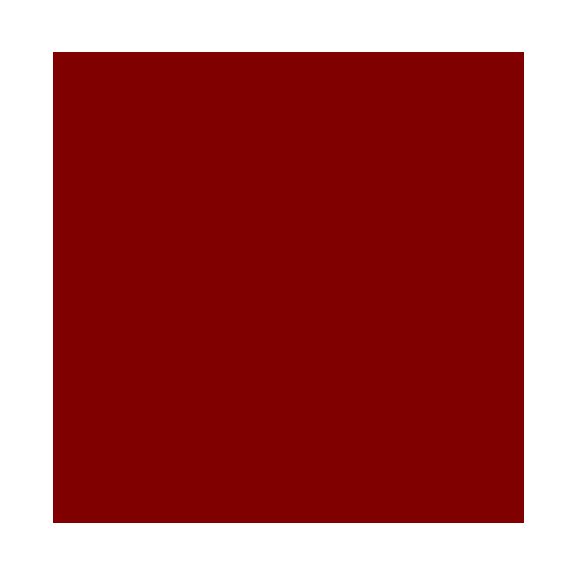

```mathematica
datavals=Union[data];
nelements =Length@datavals;
colors = {Blue, LightYellow, Green};
legend=SwatchLegend[colors,datavals]; (*{Style["1", 24],Style["2", 24]}*)
plotdata = Transpose[Partition[data,Length[Klist]]];
plot2a=ArrayPlot[plotdata,ColorRules->{1-> colors[[1]], 2-> colors[[2]], 4-> colors[[3]]}, FrameLabel-> {"K", "C_ON"}, PlotLegends -> None, BaseStyle->{FontSize-> 30}, DataReversed->True, FrameTicks-> {kticks, Conticks}, AspectRatio->1,ImageSize-> Large]
```

New plot

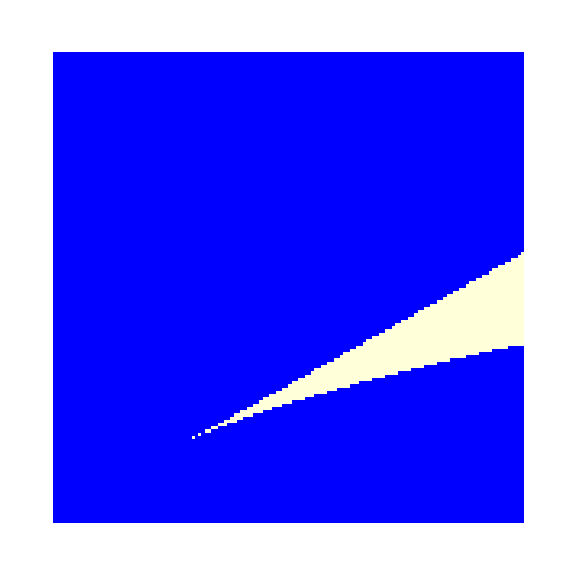

```mathematica
nelements =Length@Union[data2];
colors = {Blue,Red, LightYellow, Green};
colors = {Blue,Blue, LightYellow, Green};
legend=SwatchLegend[colors,{"Deact.", "Act.", "Act.-Deact."}];
plotdata2=Transpose@Partition[data2,Length[Klist]];
plot2b=ArrayPlot[plotdata2,ColorRules->{0-> colors[[1]], 1-> colors[[2]], 2-> colors[[3]], 4-> colors[[4]]}, FrameLabel-> {"K", "C_ON"}, PlotLegends -> None, BaseStyle->{FontSize-> 30}, DataReversed->True, FrameTicks-> {kticks, Conticks}, AspectRatio->1,ImageSize-> Large]
```

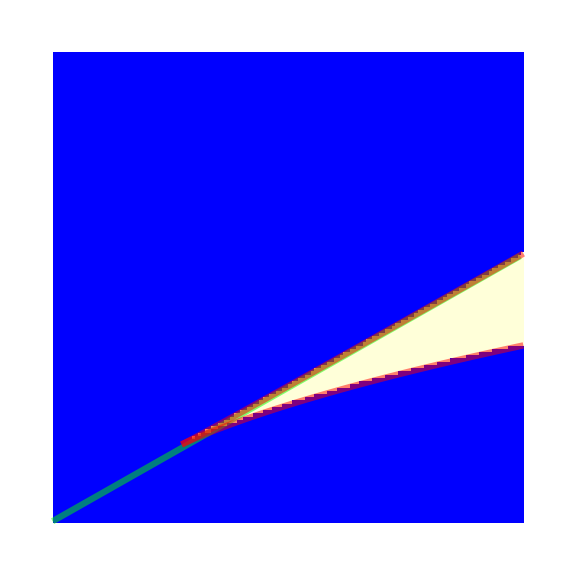

```mathematica
range= {{0,(Conmax-Constart)/ds+1},{0, (kmax-kstart)/ds+1}};
fig1=Show[plot2b,plot0b, plot1b,PlotRange-> range,ImageSize-> Large]
```

#### Export figure

```mathematica
name = "phase_diagram_n_2_strong_int_a0_0p5_Rcell_0p1_v3_temp";
fname = FileNameJoin[{NotebookDirectory[], "finite_Hill_two_cells", name}];
Export[StringJoin[fname, ".pdf"],plot1, "PDF", "ImageResolution"-> 300, "AllowRasterization"-> False]
Export[StringJoin[fname, ".eps"],plot1, "EPS", "ImageResolution"-> 300, "AllowRasterization"-> False]
```

## Dependence on a_0

Also construct a phase diagram for a_0

### Modular function (same as before)

```mathematica
allsol={};
nstablefunc[kin_,Conin_,fdin_, idx_]:=Module[{params2,nsol,J,Jn,ev,stability,tab,nstable},
Print["K = ", kin, ", Con= ", Conin, ", f(d)=", fdin];
params2 = {k-> kin, Coff-> 1, Con-> Conin, fd-> fdin, n-> 2};
nsol=NSolve[{x1 == g[x1, x2]^n/(k^n+g[x1, x2]^n),x2 == g[x2, x1]^n/(k^n+g[x2, x1]^n), x1 ∈ Reals, x2∈ Reals} /. params2, {x1,x2}];
allsol[[idx]]=nsol;
J=FullSimplify/@{{D[g[x1, x2]^n/(k^n+g[x1, x2]^n)-x1,x1],D[g[x1, x2]^n/(k^n+g[x1, x2]^n)-x1,x2]},{ D[g[x2, x1]^n/(k^n+g[x2, x1]^n)-x2,x1],D[g[x2, x1]^n/(k^n+g[x2, x1]^n)-x2,x2]}};
Jn =FullSimplify[J  /. params2];
(* Show Jacobian*) TableForm@Table[ Jn /. nsol[[i]] // MatrixForm, {i, 1, Length[nsol]}]; 
ev=Table[ Eigenvalues[Jn  /. nsol[[i]]], {i, 1, Length[nsol]}];
(*Print["Eigenvalues: (λ1, λ2)=", MatrixForm/@ev ];*)
stability = MapThread[And, Transpose@Negative[ev]];
(*Print["Eigenvalues positive?"];
tab=TableForm[stability, TableHeadings->{Table[StringReplace["Eigenvector number = %d", "%d" ->  ToString[i]], {i,1,Length[nsol]}], {"Positive?"}}];
Print[tab];*)
nstable = Total[Boole/@stability];
Print["Number of stable fixed points = ", nstable];
nstable];
ndata =1;
allsol=Range[ndata];
fdval = Exp[R-a0]/a0 Sinh[R] /. {R-> 0.1, a0->0.5};
nstablefunc[13, 30,fdval, 1]
```

### Calculate over range of a_0

```mathematica
a0all = Range[0.5, 1.5, 0.05];
ndata = Length[a0all];
fdall = Map[Exp[R-a0]/a0 Sinh[R] /. {R-> 0.1, a0->#} &, a0all];
Kall = ConstantArray[13, {ndata}];
Conall = ConstantArray[28, {ndata}];
allsol=Range[ndata];
data=MapThread[nstablefunc, {Kall, Conall, fdall, Range[ndata]}];
```

### Plot result

```mathematica
p1=ListPlot[Transpose[{fdall, data}]]
p2=ListPlot[Transpose[{a0all, data}]]
```